```mathematica
Clear[H,A,B,x1,x0,psi,out,Dmat,d1,d2,d3,d4,psi0,U,Re0,Re1,Im1,Im0]
Clear[sigX,sigZ,sigY,theta1,theta2,theta3,alpha]
(* Section used for universal objects (pauli's, H, etc.) and functions. If new functions need to be written/tested use a new cell beneath and then merge. 
*)

sigX = PauliMatrix[1];
sigY = PauliMatrix[2];
sigZ = PauliMatrix[3];
H = 1/(Sqrt[2])*{{1,1},{1,-1}};

rz[thetaZ_] := Cos[thetaZ/2]*IdentityMatrix[2] - I*Sin[thetaZ/2]*sigZ;
rx[thetaX_] :=Cos[thetaX/2]*IdentityMatrix[2] - I*Sin[thetaX/2]*sigX;

prod[psi_,phi_]:=( psi.Conjugate[phi])*(phi.Conjugate[psi]);

buildU[alpha_,theta1_,theta2_,theta3_]:= Exp[I*alpha]*rz[theta1].rx[theta2].rz[theta3];
getArgMins[psi_,phi_,params]:=Module[{Im0,Im1,Re0,Re1},
Re0 = (Re[phi[[1]]] - Re[psi[[1]]])^2;
Re1 = (Re[phi[[2]]] - Re[psi[[2]]])^2;
Im0 = (Im[phi[[1]]] - Im[psi[[1]]])^2;
Im1 = (Im[phi[[2]]] - Im[psi[[2]]])^2;
Return[NArgMin[Re0+Re1+Im0+Im1,params]];
]

getOptDmat[U_,n_] := Module[{A,B,psi,psi0,t,AtU,UtB,Dmat,d1,d2 ,d3,d4,finalMat,phi,temp,tot},
t = {0,0,0,0};
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4}];
t = t +temp  ;
];

(* Line below converts a random t to unitary t. *)
t = t/Mean[Abs[t]];
Dmat = DiagonalMatrix[t];
Return[Dmat]
];

testOptMat[Dmat_,U_,n_]:=Module[{A,B,psi,psi0,AtU,UtB,finalMat,phi,results},
results = {};
For[i=0,i<n,i++,
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
AppendTo[results,prod[phi,psi]];
];
Return[results]
]


getAverageOverlap[alpha_,theta1_,theta2_,theta3_,n_]:= Module[{U,Dmat,results},
U = buildU[alpha,theta1,theta2,theta3];

Dmat = getOptDmat[U,n];
results = testOptMat[Dmat,U,n];
Return[Mean[results]];
]


getAvgOverlapList[list_,n_]:=getAverageOverlap[list[[1]],list[[2]],list[[3]],list[[4]],n];
h[a_] := getAverageOverlap[Pi/2,a[[1]],a[[2]],Pi/2];

getStdOverlapList[list_,n_]:= Module[{U,Dmat,results},
U = buildU[list[[1]],list[[2]],list[[3]],list[[4]]];

Dmat = getOptDmat[U,n];
results = testOptMat[Dmat,U,n];
Return[StandardDeviation[results]];
]
```

```mathematica
(* NEW SECTION FOR TESTING OVER UNITARY MATRICES D
*)
getOptDmatUnit[U_,n_] := Module[{A,B,psi,psi0,t,AtU,UtB,Dmat,d1,d2 ,d3,d4,finalMat,phi,temp,tot},
t = {0,0,0,0};
For[i=0,i<n,i++,
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];

psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};

AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[{Exp[I*d1],Exp[I*d2],Exp[I*d3],Exp[I*d4]}];
finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
Print[StringForm["phi: ``",phi]];
temp = getArgMinsUnit[psi,phi,{d1,d2,d3,d4}];
t = t +temp  ;
];
Print[StringForm["Final t: ``",t/n]];
Return[DiagonalMatrix[Exp[I*t/n]]];
]

getArgMinsUnit[psi_,phi_,params_]:= Module[{psiDense,phiDense,norm,mat,f},
psiDense= Outer[Times,Conjugate[psi],psi] ;
phiDense=Outer[Times,Conjugate[phi],phi];
mat = FullSimplify[psiDense-phiDense,Table[Element[params[[i]],Reals],{i,1,Length[params]}]];
(*norm = FullSimplify[,Table[Element[params[[i]],Reals],{i,1,Length[params]}]];*)
f[x_]:=N[0.5*Sqrt[Trace[ConjugateTranspose[mat].mat]]/.params->x];
Return[NArgMin[f,params∈Cuboid[{0,0,0,0},{2Pi,2Pi,2Pi,2Pi}] ]];
]

getAverageOverlapUnit[alpha_,theta1_,theta2_,theta3_,n_]:= Module[{U,Dmat,results},
U = buildU[alpha,theta1,theta2,theta3];
Print[StringForm["U: ``",MatrixForm[U]]];
Dmat = getOptDmatUnit[U,n];
Print[StringForm["Dmat: ``",MatrixForm[Dmat]]];
results = testOptMat[Dmat,U,n];
Return[Mean[results]];
]

(*getOptDmatUnit[H,1]//MatrixForm;*)
(*getAverageOverlapUnit[Pi/2,Pi/2,Pi/2,Pi/2,1]*)
```

```mathematica
"
```

```mathematica
getOptDMat3Q[U_,n_] := Module[{A,B,d1,d2,d3,d4,d5,d6,d7,d8,t,psi,phi,psi0,Dmat,temp,AtUtU,UtUtB,finalMat},
t = {0,0,0,0,0,0,0,0};
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = TensorProduct[psi0,{1,0},{1,0}]//Flatten;
AtUtU= TensorProduct[ArrayFlatten[TensorProduct[A,U]],U]//ArrayFlatten;
UtUtB = TensorProduct[ArrayFlatten[TensorProduct[ConjugateTranspose[U],ConjugateTranspose[U]]],B]//ArrayFlatten;

Dmat = DiagonalMatrix[{d1,d2,d3,d4,d5,d6,d7,d8}];
finalMat = UtUtB.Dmat.AtUtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4,d5,d6,d7,d8}];
t = t +temp  ;
];
Return[DiagonalMatrix[t/n]];
]
testOptMat3Q[Dmat_,U_,n_]:=Module[{A,B,AtUtU,UtUtB,psi,psi0,phi,results,finalMat},
results = {};
For[i=0,i<n,i++,
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = TensorProduct[psi0,{1,0},{1,0}]//Flatten;
AtUtU= TensorProduct[ArrayFlatten[TensorProduct[A,U]],U]//ArrayFlatten;
UtUtB = TensorProduct[ArrayFlatten[TensorProduct[ConjugateTranspose[U],ConjugateTranspose[U]]],B]//ArrayFlatten;

finalMat = UtUtB.Dmat.AtUtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
AppendTo[results,prod[phi,psi]];
];
Return[results]
]
getAvgOverlap3Q[alpha_,theta1_,theta2_,theta3_,n_] := Module[{U,Dmat,results},
U = buildU[alpha,theta1,theta2,theta3];
Dmat = getOptDMat3Q[U,n];
results = testOptMat3Q[Dmat,U,n];
Print[StringForm["Matrix: ``",MatrixForm[Dmat]]];
Return[Mean[results]]
]
```

```mathematica
getOptDMat3Q[H,2]//MatrixForm
getAvgOverlap3Q[Pi/2,Pi/2,Pi/2,Pi/2,5]
```

(-0.185288 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 2.22794 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 2.95229 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.539061 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.341015 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -2.91047 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 2.42598 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.143471)

Matrix: (-0.698893 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 2.01715 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 3.37331 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.65726 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.465386 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1.62567 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 2.20903 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.04874)

1.+0. ⅈ

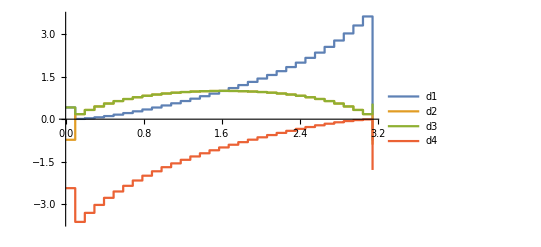

```mathematica
dx = Pi/32;
optMats = Table[Diagonal[getOptDmat[buildU[Pi/2,Pi/2,i,Pi/2],10]],{i,0,Pi,dx}];
axis = Table[i,{i,0,Pi,dx}];
Table[Table[{axis[[j]],optMats[[j]][[i]]},{j,1,Length[optMats]}],{i,1,4}];
ListPlot[%,PlotLegends->{"d1","d2","d3","d4"},Joined->True,InterpolationOrder->0]
```

```mathematica
Module[{U,n,Dmat,results},
U = buildU[Pi/2,Pi/2,Pi/2,Pi/2];
n = 100;
Dmat = getOptDmat[U,n];
results=testOptMat[Dmat,U,n];
Print[Dmat];
Print[results];
]
```

{{0.999999,0.,0.,0.},{0.,0.999998,0.,0.},{0.,0.,0.999999,0.},{0.,0.,0.,-1.}}

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

```mathematica
2^7
```

128

```mathematica
Clear[dx,dy,ay,by,ax,bx,xAxis,yAxis]
(* Code for Horizontal Section, getting profile of peak along significant axis. 
*)
dx = Pi/(2^4);
ax = Pi/2 -Pi/(2^4);
bx= Pi/2 + Pi/(2^4);

xAxis = AbsoluteTiming[Table[{i,getAvgOverlapList[{Pi/2,i,Pi/2,Pi/2},10]},{i,ax,bx,dx}]];
xAxis2 = AbsoluteTiming[Table[{i,getStdOverlapList[{Pi/2,i,Pi/2,Pi/2},10]},{i,ax,bx,dx}]];
Print[StringForm["Time Elapsed 1: ``",xAxis[[1]] + xAxis2[[1]]]];

xAxis = xAxis[[2]];
xAxis2 = xAxis2[[2]];
```

$Aborted

$Aborted

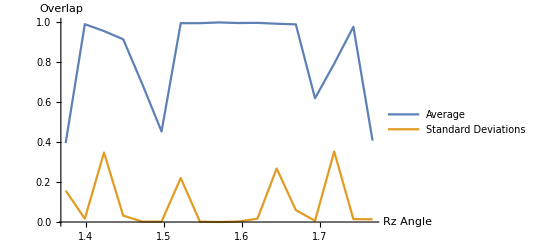

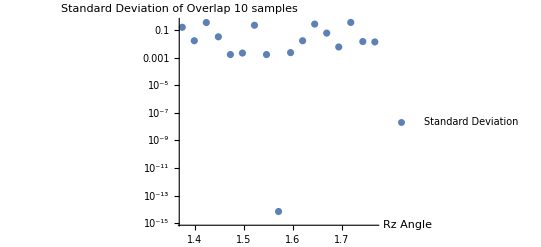

```mathematica
ListPlot[{xAxis,xAxis2},PlotLegends->{"Average","Standard Deviations"},Joined->True,AxesLabel->{"Rz Angle","Overlap"}]
ListLogPlot[xAxis2,PlotLegends-> {"Standard Deviation"},AxesLabel->{"Rz Angle","Standard Deviation of Overlap 10 samples"}]
```

```mathematica
Clear[tab0,grid,time,newTab,plotter]
dx = Pi/4;
dy = Pi/4;
ax =Pi/2 -1*dx;
bx = Pi/2 + 1*dx;
ay = Pi/2 -1*dy;
by = Pi/2+1*dy;

tab0 =  Flatten[Table[{Pi/2,i,j,Pi/2},{i,ax,bx,dx},{j,ay,by,dy}],1];
grid =  Flatten[Table[{i,j},{i,ax,bx,dx},{j,ay,by,dy}],1];
time = AbsoluteTiming[Map[getAvgOverlapList,tab0]];
Print[StringForm["Total Time elapsed: ``",time[[1]]]];
newTab = time[[2]];
plotter = Table[Append[grid[[i]],newTab[[i]]],{i,1,Length[grid]}];
```

Total Time elapsed: 8.×10^-6

```mathematica
ListDensityPlot[plotter,InterpolationOrder->0,ColorFunction->"TemperatureMap",FrameLabel->{"Rx Angle","Rz Angle"}];
ListPlot3D[{plotter,Flatten[Table[{i,j,0.5},{i,ax,bx,0.1},{j,ay,by,0.1}],1]},InterpolationOrder->10];
```

```mathematica
Clear[alpha,theta1,theta2,theta3,AtU,UtB,Dmat,A,B,a1,a2,b1,b2,psi,psi0,psi1,Dmat,d1,d2,d3,d4,params]
(*
2 QUBIT ANALYTIC SECTION.

*)
testDmatUnitary[params_,angles_] := Module[{out},
out = (Exp[I*params]/. {theta1-> angles[[1]],theta2->angles[[2]]});
Return[If[N[Abs[out]]== Table[1,{i,1,Length[out]}],1,0]];
];

psi = {psi0,0,psi1,0};

U = buildU[ Pi/2,theta1,theta2, Pi/2]//Simplify;
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];

AtU= ArrayFlatten[TensorProduct[A,U]];
UtB =ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[Exp[I*{d1,d2,d3,d4}]];
finalMat = UtB.Dmat.AtU.psi//Simplify;

(*Print["phi"]*)
phi = FullSimplify[finalMat[[1;;2]],{Element[theta1,Reals],Element[theta2,Reals]}];
(*Print["psi"];*)
psi = B.H.A.{psi0,psi1}//Simplify;

Print["Test eq1."]
eq1 = (phi[[1]] == 1/Sqrt[2]psi[[1]])/.{psi0->0,psi1-> 1}//Simplify;
eq2 = (phi[[1]] == 1/Sqrt[2]psi[[1]])/.{psi0->1,psi1->0}//Simplify;
eq3 = (phi[[2]] == 1/Sqrt[2]psi[[2]])/.{psi0->0,psi1-> 1}//Simplify;
eq4 = (phi[[2]] == 1/Sqrt[2]psi[[2]])/.{psi0->1,psi1->0}//Simplify;

params = {d1,d2,d3,d4};
params = (params/.Flatten[Normal/@Solve[{eq1,eq2,eq3,eq4},params]])//Simplify;
{d1,d2,d3,d4} = {d1,d2,d3,d4}/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0};
```

Test eq1.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Exp[I*params]

grid =Flatten[ Table[{i,j},{i,0,2Pi,Pi/64},{j,0,2Pi,Pi/64}],1];
results = Map[testDmatUnitary[params,#]&,grid];
plotter = Table[Append[grid[[i]],results[[i]]],{i,1,Length[results]}];
ListPlot3D[plotter,InterpolationOrder->1,AxesLabel->{"Theta 1","Theta 2","Test"}]
(*Plot3D[testDmatUnitary[a[{x,y}]],{x,0,2Pi},{y,0,2Pi}]*)
```

{(1/(1.+1. Cos[theta2]))^(1.+0. ⅈ),(((0.-1. ⅈ) Cos[theta1]+1. Sin[theta1]) Sin[theta2])^(-1.+0. ⅈ),(1.+0. ⅈ) (Csc[theta2]/((0.+1. ⅈ) Cos[theta1]+Sin[theta1]))^(1.+0. ⅈ),(1/(-1.+1. Cos[theta2]))^(1.+0. ⅈ)}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics3D-

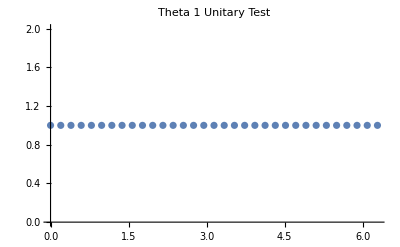

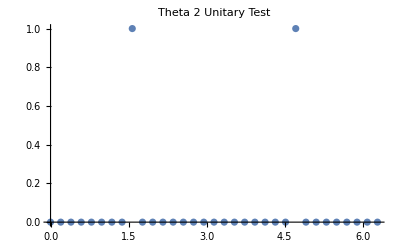

```mathematica
Off[Power::infy]
table1 =Table[{i,testDmatUnitary[params,{i,Pi/2}]},{i,0,2Pi,Pi/16}];
ListPlot[table1,PlotLabel->"Theta 1 Unitary Test"]
table2 =Table[{i,testDmatUnitary[params,{Pi/2,i}]},{i,0,2Pi,Pi/16}];
ListPlot[table2,PlotLabel-> "Theta 2 Unitary Test" ]
```

```mathematica
Clear[alpha,theta1,theta2,theta3,AtU,UtB,Dmat,A,B,a1,a2,b1,b2,psi,psi0,psi1,Dmat,d1,d2,d3,d4,params,AtUtU,UtUtB]

(*
THIS IS 3 QUBIT VERSION OF ANALYTIC EQUATION SOLVING
*)

U = buildU[Pi/2,theta1,theta2,Pi/2]
(*A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];*)

A = IdentityMatrix[2];
B = IdentityMatrix[2];

AtU= ArrayFlatten[TensorProduct[A,U]];
UtB =ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];


AtUtU = ArrayFlatten[TensorProduct[AtU,U]];

UtUtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],UtB]];


params = {d1,d2,d3,d4,d5,d6,d7,d8};
Dmat = DiagonalMatrix[Exp[I*params]];

psi = Flatten[TensorProduct[{psi0,psi1},{1,0},{1,0}]];
finalMat = FullSimplify[ UtUtB.Dmat.AtUtU,{Element[theta1,Reals],Element[theta2,Reals]}];
phi = finalMat.psi;
(*Postselection*)
Print["Phi"]
phi = phi[[1;;2]]//Normalize//Simplify
Print["psi"]
psi = B.H.A.{psi0,psi1}
```

{{((1+ⅈ) Cos[theta2/2] (Cos[theta1/2]-ⅈ Sin[theta1/2]))/(√2),((1+ⅈ) (Cos[theta1/2]-ⅈ Sin[theta1/2]) Sin[theta2/2])/(√2)},{((1-ⅈ) (Cos[theta1/2]+ⅈ Sin[theta1/2]) Sin[theta2/2])/(√2),-((1-ⅈ) Cos[theta2/2] (Cos[theta1/2]+ⅈ Sin[theta1/2]))/(√2)}}

Phi

{(2 psi0 Cos[theta2/2]^2 (-ⅇ^(ⅈ d3) (-1+Cos[theta2])+ⅇ^(ⅈ d1) (1+Cos[theta2]))+psi1 (-ⅇ^(ⅈ d7) (-1+Cos[theta2])+ⅇ^(ⅈ d5) (1+Cos[theta2])) (ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2])/(√(Abs[2 psi1 (-ⅇ^(ⅈ d8) (-1+Cos[theta2])+ⅇ^(ⅈ d6) (1+Cos[theta2])) Sin[theta2/2]^2+psi0 (-ⅇ^(ⅈ d4) (-1+Cos[theta2])+ⅇ^(ⅈ d2) (1+Cos[theta2])) (-ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2]]^2+Abs[2 psi0 Cos[theta2/2]^2 (-ⅇ^(ⅈ d3) (-1+Cos[theta2])+ⅇ^(ⅈ d1) (1+Cos[theta2]))+psi1 (-ⅇ^(ⅈ d7) (-1+Cos[theta2])+ⅇ^(ⅈ d5) (1+Cos[theta2])) (ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2]]^2)),(2 psi1 (-ⅇ^(ⅈ d8) (-1+Cos[theta2])+ⅇ^(ⅈ d6) (1+Cos[theta2])) Sin[theta2/2]^2+psi0 (-ⅇ^(ⅈ d4) (-1+Cos[theta2])+ⅇ^(ⅈ d2) (1+Cos[theta2])) (-ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2])/(√(Abs[2 psi1 (-ⅇ^(ⅈ d8) (-1+Cos[theta2])+ⅇ^(ⅈ d6) (1+Cos[theta2])) Sin[theta2/2]^2+psi0 (-ⅇ^(ⅈ d4) (-1+Cos[theta2])+ⅇ^(ⅈ d2) (1+Cos[theta2])) (-ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2]]^2+Abs[2 psi0 Cos[theta2/2]^2 (-ⅇ^(ⅈ d3) (-1+Cos[theta2])+ⅇ^(ⅈ d1) (1+Cos[theta2]))+psi1 (-ⅇ^(ⅈ d7) (-1+Cos[theta2])+ⅇ^(ⅈ d5) (1+Cos[theta2])) (ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2]]^2))}

psi

{psi0/(√2)+psi1/(√2),psi0/(√2)-psi1/(√2)}

```mathematica
Clear[Dmat]
params = {d1,d2,d3,d4,d5,d6,d7,d8};
(*eq1 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},(phi[[1]] == psi[[1]])/.{psi0->0,psi1-> 1}]//Simplify
eq2 =Assuming[{Element[theta1,Reals],Element[theta2,Reals]},(phi[[1]] == psi[[1]])/.{psi0->1,psi1->0}]//Simplify
eq3 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},(phi[[2]] == psi[[2]])/.{psi0->0,psi1-> 1}]//Simplify
eq4 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},(phi[[2]] ==psi[[2]])/.{psi0->1,psi1->0}]//Simplify*)


newGetArgMins[phi_,psi_,params_] :=Module[{eq1,eq2,eq3,eq4},
eq1 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[1]]- psi[[1]]]^2/.{psi0->0,psi1-> 1}]//Simplify;
eq2 =Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[1]] - psi[[1]]]^2/.{psi0->1,psi1->0}]//Simplify;
eq3 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[2]]- psi[[2]]]^2/.{psi0->0,psi1-> 1}]//Simplify;
eq4 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[2]] -psi[[2]]]^2/.{psi0->1,psi1->0}]//Simplify;
Return[NArgMin[eq1 + eq2 + eq3 + eq4 , params]];
]
(*params = (params/.Flatten[Normal/@Solve[{eq1,eq2,eq3,eq4},{d1,d2,d3,d4}]])//Simplify;*)

testAngles[thetaZ_,thetaX_,phi_,psi_]:=Module[{Dmat},
phi = (phi/.{theta1-> thetaZ,theta2-> thetaX})//Simplify;
Print[StringForm["Phi: ``",phi]];
Dmat = DiagonalMatrix[Exp[I*newGetArgMins[phi,psi,params]]];
Mean[Abs[testOptMat3Q[Dmat,U,10]]]//Return;
]

(*Solve[{eq1,eq2,eq3,eq4},params]
Dmat = DiagonalMatrix[Exp[I*newGetArgMins[phi,psi,params]]]
Mean[Abs[testOptMat3Q[Dmat,H,50]]]*)
(*testAngles[Pi/2,Pi/2,phi,psi]*)
```

```mathematica
f[theta1_,theta2_]:= Module[{U,AtU,UtB,AtUtU,UtUtB,params,Dmat,d1,d2,d3,d4,d5,d6,d7,d8,psi,finalMat,phi,psi0,psi1,eq1,eq2,eq3,eq4},
U = buildU[Pi/2,theta1,theta2,Pi/2];
AtU= ArrayFlatten[TensorProduct[IdentityMatrix[2],U]];
UtB =ArrayFlatten[TensorProduct[ConjugateTranspose[U],IdentityMatrix[2]]];
AtUtU = ArrayFlatten[TensorProduct[AtU,U]];
UtUtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],UtB]];


params = {d1,d2,d3,d4,d5,d6,d7,d8};
Dmat = DiagonalMatrix[Exp[I*params]];

psi = Flatten[TensorProduct[{psi0,psi1},{1,0},{1,0}]];
finalMat = FullSimplify[ UtUtB.Dmat.AtUtU,{Element[theta1,Reals],Element[theta2,Reals]}];
phi = finalMat.psi;
(*Postselection*)
phi = phi[[1;;2]]//Normalize//Simplify;
psi = H.{psi0,psi1};

eq1 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[1]]- psi[[1]]]^2/.{psi0->0,psi1-> 1}]//Simplify;
eq2 =Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[1]] - psi[[1]]]^2/.{psi0->1,psi1->0}]//Simplify;
eq3 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[2]]- psi[[2]]]^2/.{psi0->0,psi1-> 1}]//Simplify;
eq4 = Assuming[{Element[theta1,Reals],Element[theta2,Reals]},Abs[phi[[2]] -psi[[2]]]^2/.{psi0->1,psi1->0}]//Simplify;
Dmat = DiagonalMatrix[Exp[I*NArgMin[eq1+eq2+eq3+eq4,params]]];

Return[Mean[Abs[testOptMat3Q[Dmat,U,50]]]];
]
g[list_]:=f[list[[1]],list[[2]]];
Clear[i,j]
tab = Flatten[Table[{i,j},{i,Pi/4,3Pi/4,Pi/8},{j,Pi/4,3Pi/4,Pi/8}],1]
plotter = Table[Append[tab[[i]],g[tab[[i]]]],{i,1,Length[tab]}]
```

{{π/4,π/4},{π/4,(3 π)/8},{π/4,π/2},{π/4,(5 π)/8},{π/4,(3 π)/4},{(3 π)/8,π/4},{(3 π)/8,(3 π)/8},{(3 π)/8,π/2},{(3 π)/8,(5 π)/8},{(3 π)/8,(3 π)/4},{π/2,π/4},{π/2,(3 π)/8},{π/2,π/2},{π/2,(5 π)/8},{π/2,(3 π)/4},{(5 π)/8,π/4},{(5 π)/8,(3 π)/8},{(5 π)/8,π/2},{(5 π)/8,(5 π)/8},{(5 π)/8,(3 π)/4},{(3 π)/4,π/4},{(3 π)/4,(3 π)/8},{(3 π)/4,π/2},{(3 π)/4,(5 π)/8},{(3 π)/4,(3 π)/4}}

{{π/4,π/4,0.820215},{π/4,(3 π)/8,0.934828},{π/4,π/2,0.986159},{π/4,(5 π)/8,0.970304},{π/4,(3 π)/4,0.831826},{(3 π)/8,π/4,0.810433},{(3 π)/8,(3 π)/8,0.916249},{(3 π)/8,π/2,0.966799},{(3 π)/8,(5 π)/8,0.991537},{(3 π)/8,(3 π)/4,0.816553},{π/2,π/4,0.842189},{π/2,(3 π)/8,0.969057},{π/2,π/2,1.},{π/2,(5 π)/8,0.977299},{π/2,(3 π)/4,0.829312},{(5 π)/8,π/4,0.818978},{(5 π)/8,(3 π)/8,0.964671},{(5 π)/8,π/2,0.999325},{(5 π)/8,(5 π)/8,0.974757},{(5 π)/8,(3 π)/4,0.820702},{(3 π)/4,π/4,0.841518},{(3 π)/4,(3 π)/8,0.982621},{(3 π)/4,π/2,0.79593},{(3 π)/4,(5 π)/8,0.999961},{(3 π)/4,(3 π)/4,0.828142}}

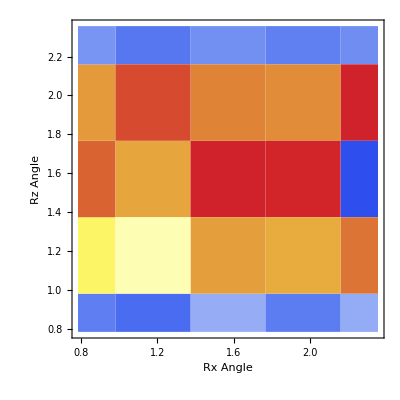

```mathematica
ListDensityPlot[plotter,InterpolationOrder->0,ColorFunction->"TemperatureMap",FrameLabel->{"Rx Angle","Rz Angle"}]
```